# Homework 5

## By Marvyn Bailly

## Question 1

### Outer Problem

Consider the ODE

```mathematica
Clear[y]
ODE = ϵ*y''[x] + (1+x)^2*y'[x] + y[x]
BC1 = y[0] - 1
BC2 = y[1] - 1
```

y[x]+(1+x)^2 y'[x]+ϵ y''[x]

-1+y[0]

-1+y[1]

Use the expansion

```mathematica
y[x_] = y0[x] + ϵ*y1[x] + ϵ^2*y2[x]
```

y0[x]+ϵ y1[x]+ϵ^2 y2[x]

Plug in the expansion

```mathematica
ODE
BC1
BC2
```

y0[x]+ϵ y1[x]+ϵ^2 y2[x]+(1+x)^2 (y0'[x]+ϵ y1'[x]+ϵ^2 y2'[x])+ϵ (y0''[x]+ϵ y1''[x]+ϵ^2 y2''[x])

-1+y0[0]+ϵ y1[0]+ϵ^2 y2[0]

-1+y0[1]+ϵ y1[1]+ϵ^2 y2[1]

Collect the first order terms

```mathematica
sol = Coefficient[ODE,ϵ,0] 
Coefficient[BC1,ϵ,0] 
right = Coefficient[BC2,ϵ,0]
```

y0[x]+y0'[x]+2 x y0'[x]+x^2 y0'[x]

-1+y0[0]

-1+y0[1]

Solve the first order ODE

```mathematica
Clear[yOut]
yOut[x_] = DSolve[{sol == 0, right == 0},y0[x],x][[1]][[1]][[2]]
yOut[0]
```

ⅇ^(-1/2+1/(1+x))

√ⅇ

Collect the second order terms

```mathematica
Coefficient[ODE,ϵ,1] 
Coefficient[BC1,ϵ,1] 
Coefficient[BC2,ϵ,1]
```

y1[x]+y1'[x]+2 x y1'[x]+x^2 y1'[x]+y0''[x]

y1[0]

y1[1]

### Inner Problem

Now we do the inner problem

```mathematica
ODE = y''[ξ] + (1+ϵ*ξ)^2*y'[ξ] + ϵ*y[ξ]
```

ϵ (y0[ξ]+ϵ y1[ξ]+ϵ^2 y2[ξ])+(1+ϵ ξ)^2 (y0'[ξ]+ϵ y1'[ξ]+ϵ^2 y2'[ξ])+y0''[ξ]+ϵ y1''[ξ]+ϵ^2 y2''[ξ]

Collecting first order terms

```mathematica
sol = Coefficient[ODE,ϵ,0] 
left = Coefficient[BC1,ϵ,0] 
Coefficient[BC2,ϵ,0]
```

y0'[ξ]+y0''[ξ]

-1+y0[0]

-1+y0[1]

Collecting second order terms

```mathematica
Coefficient[ODE,ϵ,1] 
Coefficient[BC1,ϵ,1] 
Coefficient[BC2,ϵ,1]
```

y0[ξ]+2 ξ y0'[ξ]+y1'[ξ]+y1''[ξ]

y1[0]

y1[1]

Solving the first order system gives

```mathematica
yIn = Expand[DSolve[{sol == 0,left == 0},y0[ξ],ξ]][[1]][[1]][[2]] /. C[1] -> A
```

1+A-A ⅇ^-ξ

### Matching

Now we match terms

```mathematica
match1 = Limit[yIn,ξ -> ∞]
match2 = Limit[yOut, x -> 0]
```

1+A

√ⅇ

Solving the system

```mathematica
Clear[A]
A = Solve[match1 == match2,A][[1]][[1]][[2]]
MATCH = √ⅇ
```

-1+√ⅇ

√ⅇ

Then the final solution is

```mathematica
Clear[uniSol]
uniSol[x_,ϵ_] = yIn + yOut - MATCH /. ξ -> x/ϵ
uniSol[1,0.1]
```

ⅇ^(-1/2+1/(1+x))-(-1+√ⅇ) ⅇ^(-x/ϵ)

0.999971

Plotting the solution

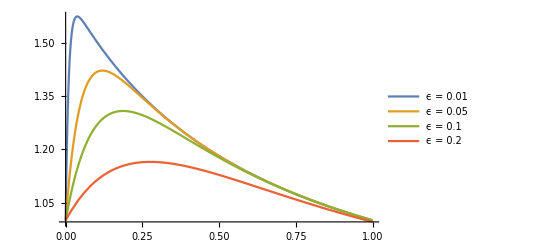

```mathematica
Plot[{uniSol[x,0.01],uniSol[x,0.05],uniSol[x,0.1],uniSol[x,0.2]},{x,0,1},PlotLegends->{"ϵ = 0.01","ϵ = 0.05","ϵ = 0.1","ϵ = 0.2"}]
```

### Inner Problem - Part B

Consider the ODE with slow var in different spot

```mathematica
y[x_] = y0[x] + ϵ*y1[x] + ϵ^2*y2[x];
ODE = y''[ξ] -(2-ϵ*ξ)^2*y'[ξ] + ϵ*y[ξ];
sol = Coefficient[ODE,ϵ,0];
Coefficient[ODE,ϵ,1]
left = Coefficient[BC1,ϵ,0] 
sol = Expand[DSolve[{sol == 0,left == 0},y0[ξ],ξ]][[1]][[1]][[2]] /. C[1] -> B
Limit[sol, ξ -> ∞]
B = 0
sol
```

y0[ξ]+4 ξ y0'[ξ]-4 y1'[ξ]+y1''[ξ]

-1+y0[0]

1-B/4+1/4 B ⅇ^(4 ξ)

B ∞

0

1

## Question 2

We consider the ODE and the boundary conditions:

```mathematica
Clear[ODE,u,L,BC1,BC2]
L = 1;
ODE[x_] = ϵ*D[u[x],{x,2}]- x^2*D[u[x],x] - u[x]
BC1 = u[0]-1
BC2 = u[L]-1
```

-u[x]-x^2 u'[x]+ϵ u''[x]

-1+u[0]

-1+u[1]

Now we look around our first boundary condition near x = 0

```mathematica
l = 0;
Expand[δ^2(ϵ*D[u[(x-l)/δ],{x,2}] - (ξ*δ)^2*D[u[(x-l)/δ],x] - u[(x-l)/δ])]
```

-δ^2 u[x/δ]-δ^3 ξ^2 u'[x/δ]+ϵ u''[x/δ]

Dropping lowest order term and balance yields: δ = ϵ^(1/2)

```mathematica
Dom1 = -δ^2 u[x]+ϵ u''[x] /. {δ -> ϵ^(1/2)}
Dom1 = - u[x]+ u''[x]
```

-ϵ (u0[x]+ϵ u1[x]+ϵ^2 u2[x])+ϵ (u0''[x]+ϵ u1''[x]+ϵ^2 u2''[x])

-u0[x]-ϵ u1[x]-ϵ^2 u2[x]+u0''[x]+ϵ u1''[x]+ϵ^2 u2''[x]

We look at the next boundary condition near x = 1

```mathematica
Clear[ξ]
l = 1;
BL2 = Simplify[δ^2(ϵ*D[u[(x-l)/δ],{x,2}] -(1-δ*ξ)^2*D[u[(x-l)/δ],x] - u[(x-l)/δ])]
```

-δ^2 u[(-1+x)/δ]-δ (-1+δ ξ)^2 u'[(-1+x)/δ]+ϵ u''[(-1+x)/δ]

Dropping lowest order term and balance yields: δ = ϵ

```mathematica
Dom2 = u'[x] + u''[x]
```

u0'[x]+ϵ u1'[x]+ϵ^2 u2'[x]+u0''[x]+ϵ u1''[x]+ϵ^2 u2''[x]

### Outer Solution

Consider the expansion

```mathematica
u[x_] = u0[x] + ϵ*u1[x] + ϵ^2*u2[x]
```

u0[x]+ϵ u1[x]+ϵ^2 u2[x]

Plugging this into the ODE yields

```mathematica
ODE[x]
BC1
BC2
```

-u0[x]-ϵ u1[x]-ϵ^2 u2[x]+x^2 (u0'[x]+ϵ u1'[x]+ϵ^2 u2'[x])+ϵ (u0''[x]+ϵ u1''[x]+ϵ^2 u2''[x])

-1+u0[0]+ϵ u1[0]+ϵ^2 u2[0]

-1+u0[1]+ϵ u1[1]+ϵ^2 u2[1]

Now collecting the leading order terms yields

```mathematica
LeadingODE = Coefficient[ODE[x],ϵ,0] 
Coefficient[BC1,ϵ,0] 
Coefficient[BC2,ϵ,0]
```

-u[x]-x^2 u'[x]

-1+u[0]

-1+u[1]

Which has the general solution

```mathematica
Clear[u]
DSolve[LeadingODE == 0,u[x],x][[1]][[1]][[2]] /. C[1] -> C
```

C ⅇ^(1/x)

### Inner Solution

First consider solution near x = 0 with δ = ϵ^(1/2), use the normal expansion, and collect leading order:

```mathematica
u[x_] = u0[x] + ϵ*u1[x] + ϵ^2*u2[x];
LeadingOrder = Coefficient[Dom1,ϵ,0] 
BC = Coefficient[BC1,ϵ,0] 
DSolve[{LeadingOrder == 0},u0[x],x][[1]][[1]][[2]][[1]]/.C[1]->A
```

-u0[x]+u0''[x]

-1+u0[0]

A ⅇ^x

Next consider solution near x = 1 with δ = ϵ, use the normal expansion, and collect leading order :

```mathematica
u[x_] = u0[x] + ϵ*u1[x] + ϵ^2*u2[x];
LeadingOrder = Coefficient[Dom2,ϵ,0] 
BC = Coefficient[BC2,ϵ,0] 
DSolve[{LeadingOrder == 0, BC==0},u0[x],x]
```

u0'[x]+u0''[x]

-1+u0[1]

{{u0[x]→ⅇ^(-1-x) (ⅇ^(1+x)-ⅇ C[1]+ⅇ^x C[1])}}

Doing lots of matching work gives the solution to be

ⅇ^((-1+x)/ϵ)+ⅇ^(-x/(√ϵ))

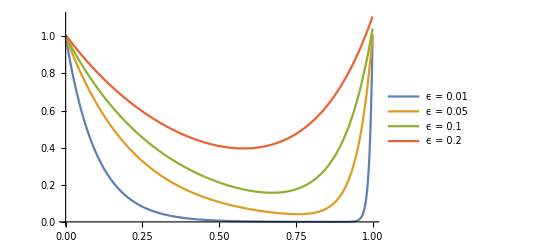

```mathematica
Clear[ϵ]
u[x_,ϵ_]=Exp[-x/ϵ^(1/2)] + Exp[-(1-x)/(ϵ)]
Plot[{u[x,0.01],u[x,0.05],u[x,0.1],u[x,0.2]},{x,0,1},PlotLegends->{"ϵ = 0.01","ϵ = 0.05","ϵ = 0.1","ϵ = 0.2"}]
```